# Lista de Exercícios 5

## Arthur Silva Magalhães - 12629595

## 1.

Vamos estudar o mapa do seno, da forma:

		                        x_(n+1)= a sin (π x_n)

Escolhendo a  = 0.75, vamos fazer os gráficos pedidos.

```mathematica
a = 0.75;
f[x_]:=a*Sin[π*x] (* Definindo a função mapa do seno *)
```

```mathematica
optam={ImageSize->Large,LabelStyle-> {"Large"}};
```

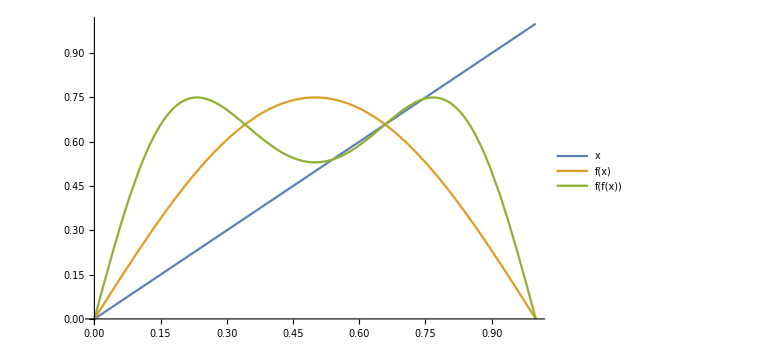

```mathematica
Plot[{x,f[x],f[f[x]]},{x,0,1},PlotLegends->"Expressions", Evaluate[optam]] (*Plotando os gráficos das funções pedidas *)
```

## 2.

Primeiramente vamos limpar os valores de f  e a  da questão anterior, para agora podermos definir uma função em que tanto o a quando x variam.

```mathematica
Clear[f,a]
```

```mathematica
f[a_][x_]:=a*Sin[π*x]
optam={ImageSize->Large,LabelStyle-> {"Large"}};
```

Agora vamos começar a definir as funções necessárias para plotarmos um Diagrama de bifurcação:

Primeiramente temos a função pontos, que irá nos gerar os pontos do diagrama de bifurcação que iremos gerar:

```mathematica
pontos:=Compile[{a,{m,_Integer},{n,_Integer}},
(
xlista=Drop[NestList[a*Sin[π*#]&,0.5,n],m+1];
saida={};
Do[AppendTo[saida,{a,xlista[[i]]}],{i,1,Length[xlista]}];
saida
),{{saida,_Real,2}}]
```

Agora uma função que irá “varrer” estes pontos entre valores de a a serem definidos:

```mathematica
varrepontos:=Compile[{amin,amax,na,{m,_Integer},{n,_Integer}},
(
grandelista={};
Do[AppendTo[grandelista,pontos[a,m,n]],{a,amin,amax,(amax-amin)/na}];
Flatten[grandelista,1]
),{{grandelista,_Real,3}}]
```

Finalmente temos a função que irá nos gerar o diagrama de bifurcação correspondente:

```mathematica
diagbifurca[amin_,amax_,na_,m_,n_]:=ListPlot[varrepontos[amin,amax,na,m,n],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotStyle->PointSize[0.001],AspectRatio->1,Evaluate[optam]]
```

```mathematica
diagbifurca[0,1,1000,1024,2048]
```

-Graphics-

## 3.

Agora vamos encontrar os menores valores de a (entre 0 e 1), que tornam instáveis os ciclos com período n entre 2 e 218.

Repare que no gráfico da questão anterior já podemos identificar claramente 3 destes pontos, e vamos utilizar a função FindRoot, juntamente com a ferramenta de Get Coordinates do gráfico, para podermos dar um chute inicial bem próximo do valor real, então o FindRoot conseguirá determina-lo com precisão de máquina.

```mathematica
est1=FindRoot[{x==Nest[f[a],x,1],D[Nest[f[a],x,1],x]==-1},{{x,0.64},{a,0.72}}]  (* Este não é necessário, pois vamos avalaiar somente os períodos n de 2 até 128 *)
```

{x→0.645774,a→0.719962}

```mathematica
est2=FindRoot[{x==Nest[f[a],x,2],D[Nest[f[a],x,2],x]==-1},{{x,0.45},{a,0.83}}]
```

{x→0.444794,a→0.833266}

```mathematica
est4=FindRoot[{x==Nest[f[a],x,4],D[Nest[f[a],x,4],x]==-1},{{x,0.37},{a,0.85}}]
```

{x→0.373868,a→0.858609}

Agora que já coletamos os 3 primeiros valores de a (0.719962 ; 0.833266 ;0.858609) precisaremos ampliar o gráfico na região da próxima bifurcação de modo a podermos encontrar as coordenadas do próximos pontos. Temos então:

```mathematica
Show[diagbifurca[0.82,0.87,1000,1024,2048],PlotRange->{0.35,0.4}]
```

-Graphics-

-Graphics-

```mathematica
est8=FindRoot[{x==Nest[f[a],x,8],D[Nest[f[a],x,8],x]==-1},{{x,0.358},{a,0.864}}]
```

{x→0.358643,a→0.864084}

```mathematica
est16=FindRoot[{x==Nest[f[a],x,16],D[Nest[f[a],x,16],x]==-1},{{x,0.355},{a,0.865}}]
```

{x→0.355552,a→0.865259}

Temos agora os seguintes valores de a (0.864084 ; 0.865259) , e devemos ainda ampliar mais uma vez para que possamos encontrar o os pontos dos ciclos de 32, 64 e 128. Temos então:

```mathematica
Show[diagbifurca[0.8654,0.8656,1000,1024,2048],PlotRange->{0.3545,0.3550}]
```

-Graphics-

```mathematica
0.865565
```

0.865565

```mathematica
est32=FindRoot[{x==Nest[f[a],x,32],D[Nest[f[a],x,32],x]==-1},{{x,0.354928},{a,0.865505}}]
```

{x→0.354924,a→0.865511}

```mathematica
est64=FindRoot[{x==Nest[f[a],x,64],D[Nest[f[a],x,64],x]==-1},{{x,0.354782},{a,0.865569}}]
```

{x→0.354796,a→0.865565}

```mathematica
est128=FindRoot[{x==Nest[f[a],x,128],D[Nest[f[a],x,128],x]==-1},{{x,0.354788},{a,0.865575}}]
```

{x→0.354786,a→0.865576}

Assim encontrarmos os últimos valores de a que queríamos encontrar, de valores (0.865511 ; 0.865565;0.865576).

## 4.

Agora vamos criar uma tabela com os valores de a encontrados para os períodos de 2 a 128:

```mathematica
m = {{2^j,a},  {2, 0.833266}, {4,0.858609 }, {8,0.864084}, {16,0.865259}, {32,0.865511}, {64,0.865565}, {128,0.865576}};
```

```mathematica
Grid[m,Frame->All]
```

2^j | a
2 | 0.833266
4 | 0.858609
8 | 0.864084
16 | 0.865259
32 | 0.865511
64 | 0.865565
128 | 0.865576

Agora vamos fazer consecutivos valores de príodos subsequentes para obter estimativas da constante δ de Feigenbaum.

```mathematica
δest0=((a/. est4)-(a/. est2))/((a/. est8)-(a/. est4));
NumberForm[δest0,10]
```

4.628708562

```mathematica
δest1=((a/. est8)-(a/. est4))/((a/. est16)-(a/. est8));
NumberForm[δest1,10]
```

4.660516216

```mathematica
δest2=((a/. est16)-(a/. est8))/((a/. est32)-(a/. est16));
NumberForm[δest2,10]
```

4.667351591

```mathematica
δest3=((a/. est32)-(a/. est16))/((a/. est64)-(a/. est32));
NumberForm[δest3,10]
```

4.668804538

```mathematica
δest4=((a/. est64)-(a/. est32))/((a/. est128)-(a/. est64));
NumberForm[δest4,10]
```

4.669116692

Perceba que para cada valor consecutivo que fazemos obtemos um valor mais próximo, em 10 casas decimais, de valor fornecido de δ_log= 4.669201609.

## 5.

Primeiramente vamos encontrar os valores de Δ_j (j = 3,4,5,6), depois vamos plotar um gráfico com os respectivos pontos {j,Δ_j }:

```mathematica
optam={ImageSize->Large,LabelStyle-> {"Large"}};
```

```mathematica
δ= 4.669201609
```

4.6692

```mathematica
Δj3 = 4.669201609-  "4.660516216"
```

0.00868539

```mathematica
Δj4 = 4.669201609-  "4.667351591"
```

0.00185002

```mathematica
Δj5 = 4.669201609-  "4.668804538"
```

0.000397071

```mathematica
Δj6 = 4.669201609-  "4.669116692"
```

0.0000849171

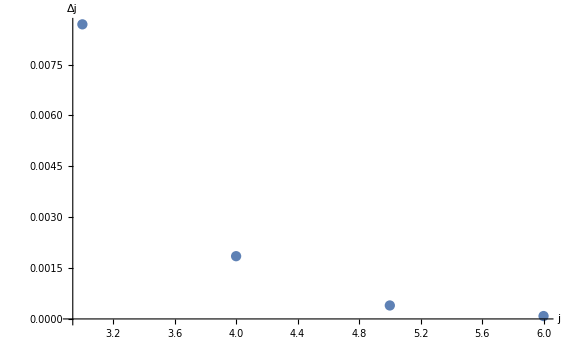

```mathematica
plot1  = ListPlot[{{3,0.008685392820201976},{4,0.0018500184909608919},{5,0.0003970709427356667},{6,0.00008491707920477154}}, AxesLabel->{"j","Δj" }, Evaluate[optam]]
```

Agora plotado os pontos, iremos encontrar os parâmetros a e b para ajustarmos uma função exponencial do tipo a*Exp[-b*j].  Temos então:

```mathematica
datalist = {{3,0.008685392820201976},{4,0.0018500184909608919},{5,0.0003970709427356667},{6,0.00008491707920477154}}; (* Definindo a lista de pontos o gráfico *)
```

```mathematica
nln = NonlinearModelFit[datalist,a*Exp[-b*j],{a,b},j](* Encontrando os parâmetros do modelo exponencial *)
```

FittedModel[0.896962 ⅇ^(-1.5458 j)]

Os parâmetros encontrados são então a = 0.896962 e b = 1.5458 .

```mathematica
nln[j]
```

0.896962 ⅇ^(-1.5458 j)

O gráfico do ajuste é da forma:

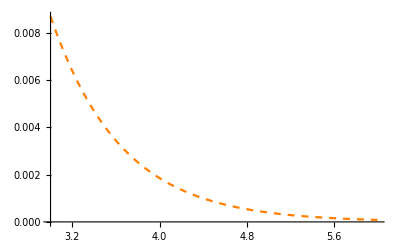

```mathematica
plot2 =Plot[nln[j], {j,3,6}, PlotStyle->{Orange,Dashed}]
```

Juntando ambos os gráficos temos então o resultado do ajuste aos pontos da forma:

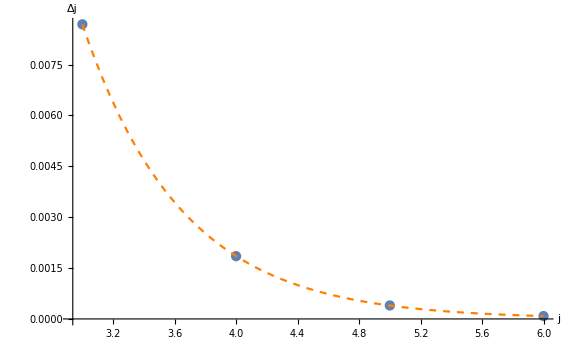

```mathematica
Show[{plot1,plot2}]
```

## 6.

Primeiro vamos definir a função para encontrarmos o coeficiente de Lyapunov:

```mathematica
lyapunov[a_,x0_,n_,m_]:=
(xlista=Drop[NestList[f[a],x0,n],m+1];
Total[Log[Abs[f[a]'[xlista]]]]/Length[xlista]
)
```

```mathematica
lyapunov[1,0.5,10000,1000]
```

0.690016

Portanto, para a=1 temos o coeficiente de Lyapunov de 0.690

Vamos agora plotar o gráfico para o coeficiente com a variando entre 0.5 e 1 :

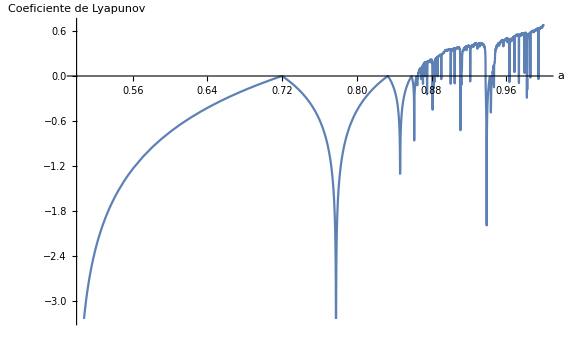
{59.3302,-Graphics-}

```mathematica
Plot[lyapunov[a,0.5,10000,1000],{a,0.5,1},Evaluate[optam],AxesLabel-> {"a","Coeficiente de Lyapunov"}]//Timing
```

Usando o Get Coordinates, podemos perceber que o regime caótico começa a partir da vizinhança do ponto {0.8610,-0.00163}